```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/mike/Documents/Data/Photochemical Data/From_Justin/uv/uvxsect

```mathematica
co2edat=Import["CO2_swri.txt","Table"][[56;;]];
```

```mathematica
co2branchnames=Import["CO2_swri.txt","Table"][[55]]
```

{Lambda,Total,sCO/O1D,CO2+,CO+O,O+CO,C+O2,sCO/O,tCO/O}

```mathematica
co2edat//Dimensions
```

{534,9}

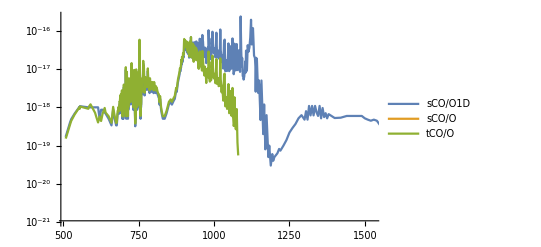

```mathematica
ListLogPlot[Association@@MapThread[Rule,{co2branchnames[[3;;]],{co2edat[[;;,1]],#}ᵀ&/@(co2edat[[;;,3;;]]ᵀ)}][[{1,-2,-1}]],Joined->True,PlotRange->{10^-21,All}]
```

```mathematica
co2einterp[λ_]=Exp[Interpolation[{co2edat[[;;,1]],Log/@((Total/@co2edat[[;;,{4,5,6,7}]])/.(0.->10^-35.))}ᵀ,InterpolationOrder->1][λ]]
```

ⅇ^(InterpolatingFunction[{{1., 2275.}}, <>][λ])

```mathematica
binnedco2e=Function[bin,{Mean[bin],NIntegrate[co2einterp[λ],{λ,bin[[1]],bin[[2]]}]/(bin[[2]]-bin[[1]])}]/@Table[{0,10}+ii,{ii,0,2270,10}];
```

```mathematica
co2ephoto={co2edat[[;;,1]],Total/@co2edat[[;;,{4,5,6,7}]]}ᵀ;
```

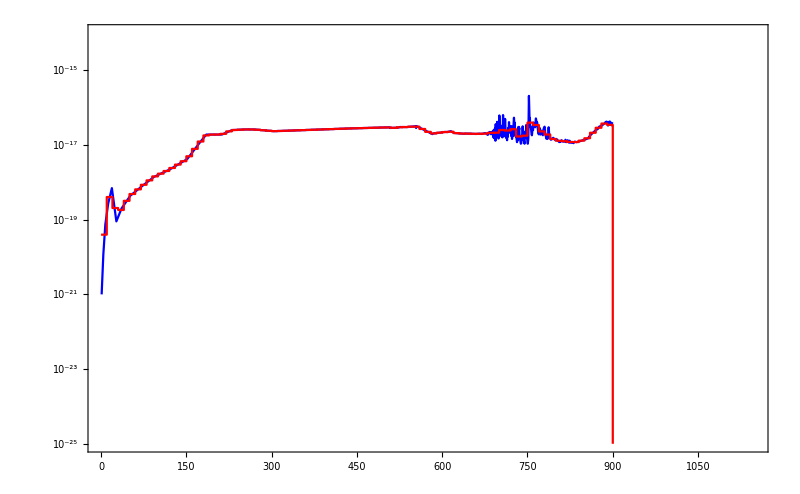

```mathematica
ListLogPlot[{co2ephoto,Flatten[{{#[[1]]-5,#[[2]]},{#[[1]]+5,#[[2]]}}&/@binnedco2e,1]},PlotRange->{{0,1150},{10^-25,10^-14}},Frame->True,Joined->True,InterpolationOrder->1,ImageSize->800,PlotStyle->{Blue,Red}]
```

```mathematica
Export["binnedCO2e.csv",{0.1,1}*#&/@binnedco2e]
```

binnedCO2e.csv

```mathematica
co2interp[λ_]=Exp[Interpolation[{co2edat[[;;,1]],Log/@((Total/@co2edat[[;;,{3,-1,-2}]])/.(0.->10^-35.))}ᵀ,InterpolationOrder->1][λ]]
```

ⅇ^(InterpolatingFunction[{{1., 2275.}}, <>][λ])

```mathematica
binnedco2=Function[bin,{Mean[bin],NIntegrate[co2interp[λ],{λ,bin[[1]],bin[[2]]}]/(bin[[2]]-bin[[1]])}]/@Table[{0,10}+ii,{ii,0,2270,10}];
```

```mathematica
co2photo={co2edat[[;;,1]],Total/@co2edat[[;;,{3,-1,-2}]]}ᵀ;
```

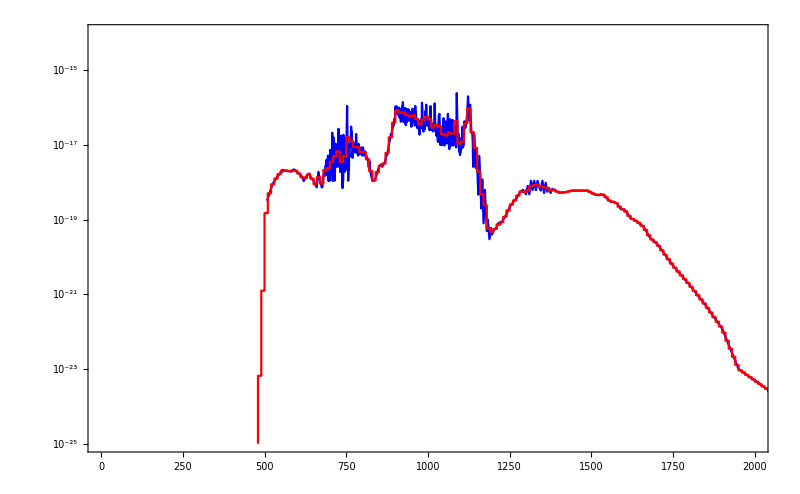

```mathematica
ListLogPlot[{co2photo,Flatten[{{#[[1]]-5,#[[2]]},{#[[1]]+5,#[[2]]}}&/@binnedco2,1]},PlotRange->{{0,2000},{10^-25,10^-14}},Frame->True,Joined->True,InterpolationOrder->1,ImageSize->800,PlotStyle->{Blue,Red}]
```

```mathematica
Export["binnedCO2_dissociation_swri.csv",{0.1*binnedco2[[;;,1]],binnedco2[[;;,2]],binnedco2[[;;,2]]}ᵀ]
```

binnedCO2_dissociation_swri.csv

```mathematica
h2dat=Import["H2.txt","Table"][[48;;]];
```

```mathematica
h2dat[[51,1]]+=0.0001
```

844.8

```mathematica
h2interp[λ_]=Exp[Interpolation[{h2dat[[;;,1]],Log/@((Total/@h2dat[[;;,{3,4}]])/.(0.->10^-35.))}ᵀ,InterpolationOrder->1][λ]]
```

ⅇ^(InterpolatingFunction[{{1.,2768.8}},<>][λ])

```mathematica
binnedh2=Function[bin,{Mean[bin],NIntegrate[h2interp[λ],{λ,bin[[1]],bin[[2]]}]/(bin[[2]]-bin[[1]])}]/@Table[{0,10}+ii,{ii,0,2760,10}];
```

```mathematica
h2photo={h2dat[[;;,1]],Total/@h2dat[[;;,{3,4}]]}ᵀ;
```

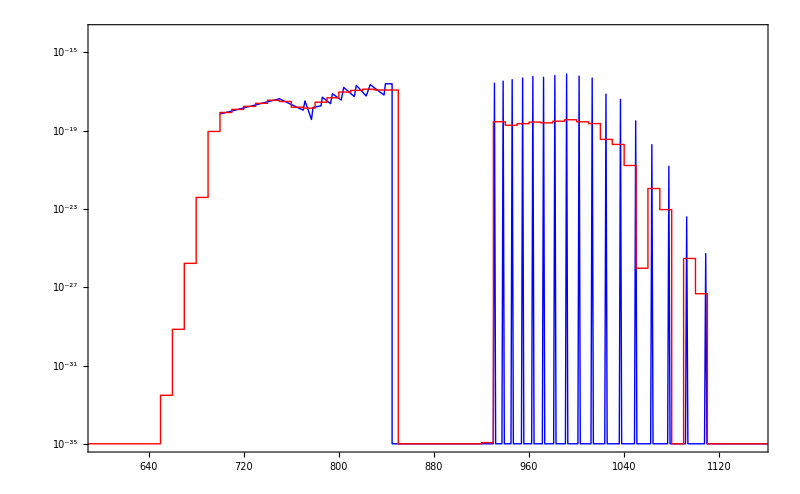

```mathematica
ListLogPlot[{h2photo,Flatten[{{#[[1]]-5,#[[2]]},{#[[1]]+5,#[[2]]}}&/@binnedh2,1]},PlotRange->{{600,1150},{10^-35,10^-14}},Frame->True,Joined->True,InterpolationOrder->1,ImageSize->800,PlotStyle->{Blue,Red}]
```

```mathematica
Export["binnedH2.csv",{0.1,1}*#&/@binnedh2]
```

binnedH2.csv

```mathematica
ohdat=Import["OH.txt","Table"][[22;;]];
```

```mathematica
Import["OH.txt","Table"][[21]]
```

{Lambda,Total,O/H,O1S/H,OH+,O1D/H}

```mathematica
Position[ohdat,5114.]
```

{{62,1},{63,1}}

```mathematica
ohdat[[63,1]]+=0.01
```

5114.01

```mathematica
ohinterp[λ_]=Exp[Interpolation[{ohdat[[;;,1]],Log/@((Total/@ohdat[[;;,{3,4}]])/.(0.->10^-35.))}ᵀ,InterpolationOrder->1][λ]]
```

ⅇ^(InterpolatingFunction[{{0.6,61320.}},<>][λ])

```mathematica
binnedoh=Function[bin,{Mean[bin],NIntegrate[ohinterp[λ],{λ,bin[[1]],bin[[2]]}]/(bin[[2]]-bin[[1]])}]/@Table[{0,10}+ii,{ii,0,6000,10}];
```

```mathematica
ohphoto={ohdat[[;;,1]],Total/@ohdat[[;;,{3,4}]]}ᵀ;
```

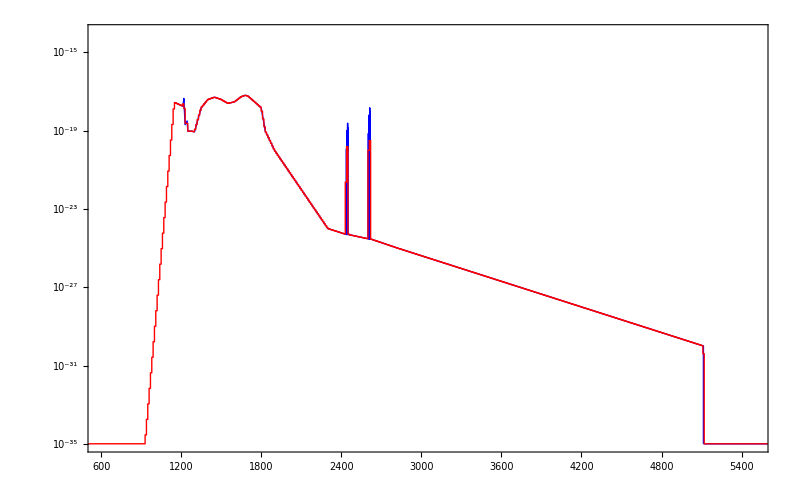

```mathematica
ListLogPlot[{ohphoto,Flatten[{{#[[1]]-5,#[[2]]},{#[[1]]+5,#[[2]]}}&/@binnedoh,1]},PlotRange->{{600,5500},{10^-35,10^-14}},Frame->True,Joined->True,InterpolationOrder->1,ImageSize->800,PlotStyle->{{Thick,Blue},Red}]
```

```mathematica
Export["binnedOH.csv",{0.1,1}*#&/@binnedoh]
```

binnedOH.csv

```mathematica
oho1Dinterp[λ_]=Exp[Interpolation[{ohdat[[;;,1]],Log/@((Total/@ohdat[[;;,{5}]])/.(0.->10^-35.))}ᵀ,InterpolationOrder->1][λ]]
```

ⅇ^(InterpolatingFunction[{{0.6,61320.}},<>][λ])

```mathematica
binnedoho1D=Function[bin,{Mean[bin],NIntegrate[oho1Dinterp[λ],{λ,bin[[1]],bin[[2]]}]/(bin[[2]]-bin[[1]])}]/@Table[{0,10}+ii,{ii,0,6000,10}];
```

```mathematica
oho1Dphoto={ohdat[[;;,1]],Total/@ohdat[[;;,{5}]]}ᵀ;
```

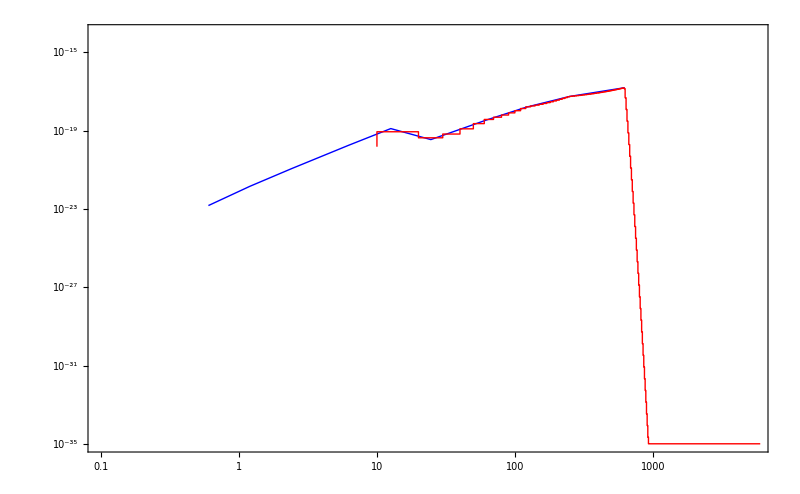

```mathematica
ListLogLogPlot[{oho1Dphoto,Flatten[{{#[[1]]-5,#[[2]]},{#[[1]]+5,#[[2]]}}&/@binnedoho1D,1]},PlotRange->{{0.1,5500},{10^-35,10^-14}},Frame->True,Joined->True,InterpolationOrder->1,ImageSize->800,PlotStyle->{{Thick,Blue},Red}]
```

```mathematica
Export["binnedOHo1D.csv",{0.1,1}*#&/@binnedoho1D]
```

binnedOHo1D.csv

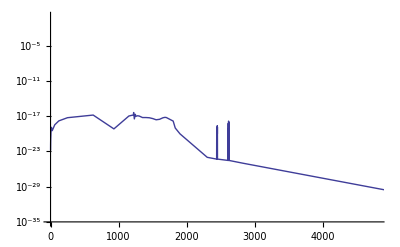

```mathematica
ListLogPlot[ohdat[[;;,{1,2}]],Joined->True]
```

```mathematica
{CO2195,CO2295}=Import["CO2.dat"][[4;;]]ᵀ[[#]]ᵀ&/@{{1,2},{1,3}};
```

```mathematica
H2O=Import["H2O.dat"][[4;;]];
```

```mathematica
O2=Import["O2.dat"][[4;;]];
```

```mathematica
O2schrungdat1=Import["130-190.cf4","Table"];
O2schrungdat2=Import["190-280.cf4","Table"];
O2schrungdat3=Import["280-500.cf4","Table"];
```

```mathematica
o2tab[T_]=Table[
{Mean[#[[1]]],10^-20*Total[#[[2]]]}&@(Select[#,bλ<#[[1]]<bλ+1&]ᵀ)
,{bλ,175,204}]&/@{{10^7./#[[1]],#[[2]]((T-100)/10)^4+#[[3]]*((T-100)/10)^2+#[[4]]}&/@O2schrungdat1[[4;;]],{10^7./#[[1]],#[[2]]((T-100)/10)^4+#[[3]]*((T-100)/10)^2+#[[4]]}&/@O2schrungdat1[[4;;]],{10^7./#[[1]],#[[2]]((T-100)/10)^4+#[[3]]*((T-100)/10)^2+#[[4]]}&/@O2schrungdat3[[4;;]]};
```

```mathematica
O2schrung[T_]:=Which[
130≤T<190,o2tab[T][[1]],
190≤T<280,o2tab[T][[2]],
280≤T<500,o2tab[T][[3]]
]
```

```mathematica
binnedO2schrung[T_][λ_]:=If[176<λ<204,
Interpolation[O2schrung[T]][λ] λ^2*0.5*^-7
,0]
```

```mathematica
herzmann[λ_]:=10^-24*If[λ>192,{-2.3837947*^4,4.1973085*^2,-2.7640139*^0,8.0723193*^-3,-8.8255447*^-6}.{1,λ,λ^2,λ^3,λ^4},0]
```

```mathematica
O2Tx[T_]:={O2[[;;,1]],O2[[;;,2]]+(binnedO2schrung[T][#]&/@O2[[;;,1]])+(herzmann[#]&/@O2[[;;,1]])}ᵀ
```

```mathematica
Manipulate[ListLogPlot[O2Tx[T],Joined->True,PlotRange->All],{T,130,499}]
```

ListLogPlot::lpn: O2Tx[130] is not a list of numbers or pairs of numbers.

ListLogPlot::lpn: O2Tx[130.] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLogPlot::lpn will be suppressed during this calculation.

```mathematica
O3=Import["O3.dat"][[4;;]];
```

```mathematica
O3chap={1.*^7/#[[1]],#[[2]]}&/@Import["O3Chap.dat"][[4;;]];
```

```mathematica
?Histogram
```

RowBox[{"Histogram", "[", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "]"}] plots a histogram of the values SubscriptBox[StyleBox["x", "TI"], StyleBox["i", "TI"]].
RowBox[{"Histogram", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["bspec", "TI"]}], "]"}] plots a histogram with bin width specification StyleBox["bspec", "TI"].
RowBox[{"Histogram", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["bspec", "TI"], ",", StyleBox["hspec", "TI"]}], "]"}] plots a histogram with bin heights computed according to the specification StyleBox["hspec", "TI"].
RowBox[{"Histogram", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["data", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["data", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["…", "TR"]}], "]"}] plots histograms for multiple datasets SubscriptBox[StyleBox["data", "TI"], StyleBox["i", "TI"]].

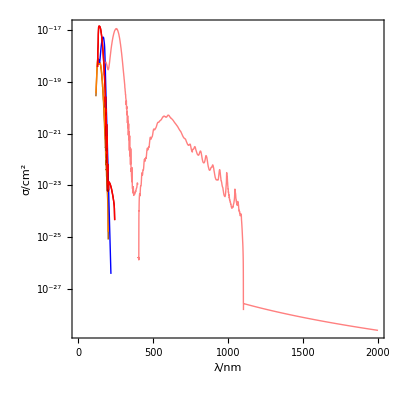

```mathematica
ListLogPlot[{CO2195,CO2295,H2O,O2Tx[195],O2Tx[295],O3,O3chap},Joined->True,Frame->True,AspectRatio->1,PlotStyle->({Thick,#}&/@{Darker[Orange],Orange,Blue,Darker[Red],Red,Pink,Pink}),FrameStyle->Thick,LabelStyle->16,ImageSize->400,FrameLabel->{"λ/nm","σ/cm^2"}]
```

```mathematica
h2oalt=Import["h2oavgtbl.dat","Table"][[4;;]];
```

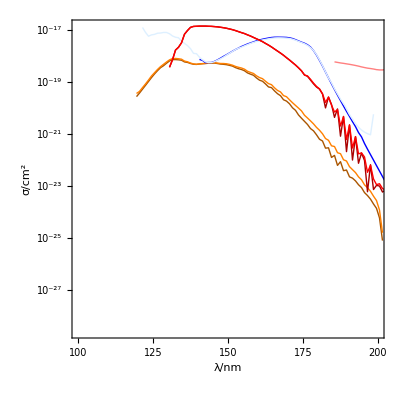

```mathematica
ListLogPlot[{CO2195,CO2295,H2O,h2oalt,O2Tx[195],O2Tx[295],O3,O3chap},Joined->True,Frame->True,AspectRatio->1,PlotStyle->({Thick,#}&/@{Darker[Orange],Orange,Blue,LightBlue,Darker[Red],Red,Pink,Pink}),FrameStyle->Thick,LabelStyle->16,ImageSize->400,FrameLabel->{"λ/nm","σ/cm^2"},PlotRange->{{100,200},All}]
```